# Examples of how to use Mathematica

Mathematica is a powerful piece of computational algebra software (which can also do a lot more!). In this notebook we look at a few examples. The notebook mirrors the SymPy example notebook that can also be found in this repository.

### Defining equations

```mathematica
a = (x+x^2)/(x Sin[y]^2+x Cos[y]^2)
```

(x+x^2)/(x Cos[y]^2+x Sin[y]^2)

```mathematica
b=x^2+1
```

1+x^2

```mathematica
b-1
```

x^2

### Simplification

```mathematica
a=((x-2)(x+3))/((x-2)(x-9))
```

(3+x)/(-9+x)

```mathematica
a=(x^2+x-6)/(x^2-11x+18)
```

(-6+x+x^2)/(18-11 x+x^2)

```mathematica
Simplify[a]
```

(3+x)/(-9+x)

```mathematica
b = (x+x^2)/(x Sin[y]^2+x Cos[y]^2)
```

(x+x^2)/(x Cos[y]^2+x Sin[y]^2)

```mathematica
Simplify[b]
```

1+x

### Differentiation

```mathematica
a = x^2+3x+4 y^2
```

3 x+x^2+4 y^2

```mathematica
D[a,x]
```

3+2 x

```mathematica
D[a,y]
```

8 y

```mathematica
D[ArcSinh[x],x]
```

1/(√(1+x^2))

```mathematica
res=D[(x^2+x-6)/(x^2-11x+18),x]
Simplify[res]
```

(1+2 x)/(18-11 x+x^2)-((-11+2 x) (-6+x+x^2))/((18-11 x+x^2)^2)

-12/(-9+x)^2

### Integration

```mathematica
a = x/(x^2+2x+1);
Integrate[a,x]
```

1/(1+x)+Log[1+x]

```mathematica
b=Integrate[Sin[x],{x,0,3}]
```

1-Cos[3]

```mathematica
N[b]
N[b,50]
```

1.98999

1.9899924966004454572715727947312613023936790966156

Sometimes operations will return non-elementary functions:

```mathematica
res=Integrate[Cos[x]/(x^2+1),{x,1,5}]
```

1/(4 ⅇ)(-ⅈ (1+ⅇ^2) CosIntegral[-5+ⅈ]+ⅈ (1+ⅇ^2) CosIntegral[-1+ⅈ]-ⅈ (1+ⅇ^2) CosIntegral[1+ⅈ]+ⅈ (1+ⅇ^2) CosIntegral[5+ⅈ]-(-1+ⅇ^2) (SinIntegral[-1+ⅈ]-SinIntegral[1+ⅈ])+(-1+ⅇ^2) (SinIntegral[-5+ⅈ]-SinIntegral[5+ⅈ]))

```mathematica
N[res]
```

-0.139801+0. ⅈ

#### Solving equations

```mathematica
Solve[(x-2)(x+3)==0,x]
```

{{x→-3},{x→2}}

```mathematica
Solve[x^2+x-1==0,x]
```

{{x→1/2 (-1-√5)},{x→1/2 (-1+√5)}}

## Derive the weights for Simpson’s method

```mathematica
P2[x_]:=f[a]((x-b)(x-c))/((a-b)(a-c))+f[b]((x-a)(x-c))/((b-a)(b-c))+f[c]((x-a)(x-b))/((c-a)(c-b))
```

```mathematica
integral=Integrate[P2[x],{x,a,b}]
```

((a-b) ((2 a+b-3 c) (b-c) f[a]+(a+2 b-3 c) (a-c) f[b]-(a-b)^2 f[c]))/(6 (a-c) (-b+c))

```mathematica
Simplify[integral/.c->(a+b)/2]
```

-1/6 (a-b) (f[a]+f[b]+4 f[(a+b)/2])

## Neat examples

Below are some additional examples of the power of Mathematica

### Solving ODEs

```mathematica
s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[…]}}

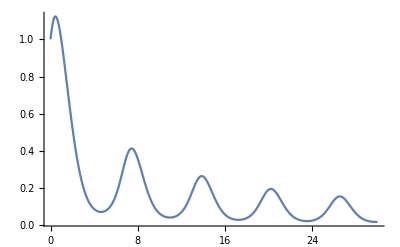

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]
```

### Numerical Integration

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,2}]
```

1.24706

### 3D plots

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

### Manipulate

```mathematica
Manipulate[Plot[Sin[x(1+a x)],{x,0,6}],{a,0,2}]
```

### Image identification with neural networks

```mathematica
ImageIdentify[-Graphics-]
```

hound

```mathematica
ImageIdentify[-Graphics-]
```

domestic cat

```mathematica
ImageIdentify[-Graphics-]
```

sail